# Cálculo de observables de estrellas compactas esféricas

Adriel Ernesto Rodríguez Concepción

Facultad de Física, Universidad de La Habana, Cuba.
Instituto de Cibernética, Matemática y Física (ICIMAF), La Habana, Cuba.

Este programa está diseñado para calcular todos los observables que sé calcularles a estrellas no magnetizadas, estáticas y estacionarias compuestas por un fluido isotrópico autogravitante. Calcula masa, radio, momento de inercia, segundo número de Love k_2, el parámetro adimensional de deformación de mareas Λ, el corrimiento al rojo gravitacional de las ondas electromagnéticas emitidas en la superficie, y la masa bariónica. El programa recibe una tabla con la ecuación de estado (barotrópica) y devuelve una tabla con los observables de  toda una secuencia de estrellas con dicha densidad central.

10 de febrero de 2024

```mathematica
SetDirectory[NotebookDirectory[]]
(*Le decimos a Mathematica que guarde y lea de archivos que estan en el mismo directorio qu este cuaderno*)
```

/home/adriel/Desktop/laptop mia/trabajos/Tidal deformability Gamma

```mathematica
(*Importamos el archivo con la EdE que vamos a utilizar. El mismo debe contener una tabla de 5 columnas que contengan:


E  P_(||)  P_⊥ ρ  Subscript[N, b]

con la energia y las presiones en MeV^4, la densidad en g/cm^3 y el numero de particulas por unidad de volumen en MeV^3.
La variable filename almacenara el nombre de dicho archivo.
*)
filename = "bosons_T0_B0_a5.dat";
EoS = Import[filename,"Table"];
Edat = EoS[[All,1]];
Pdat = EoS[[All,2]];
Rhodat = EoS[[All,4]];
EvsPdat = Transpose[{Pdat,Edat}];
```

```mathematica
(*Sacamos el minimo valor de presion que se puede usar dentro de una estrella*)
Pmin= Max[0, Min[Pdat]]
```

3.56073

```mathematica
(*Ahora vamos a crear un interpolador que nos de la densidad de energia como funcion de la presion*)
Energy = Interpolation[EvsPdat]
BarionicDensity = Interpolation[Transpose[{Pdat,Rhodat}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Length[EoS]
```

5001

```mathematica
(*Aqui vamos  a obtener los valores de la HeatFunction que usaremos en la primera integral de movimiento del fluido. Se demoran en calcular. Ten paciencia.*)
```

```mathematica
Hdat=Table[0.,Length[EoS]];
Hdat[[1]] = NIntegrate[1/(Energy[x]+x),{x,Pmin,Pdat[[1]]}]
For[i = 2, i ≤ Length[Pdat], i++,
Hdat[[i]] = Hdat[[i-1]] +  NIntegrate[1/(Energy[x]+x),{x,Pdat[[i-1]],Pdat[[i]]}];
Print[i]
]
```

0.

```mathematica
(*Y su interpolador*)
HeatFunction= Interpolation[Transpose[{Pdat,Hdat}]]
```

InterpolatingFunction[…]

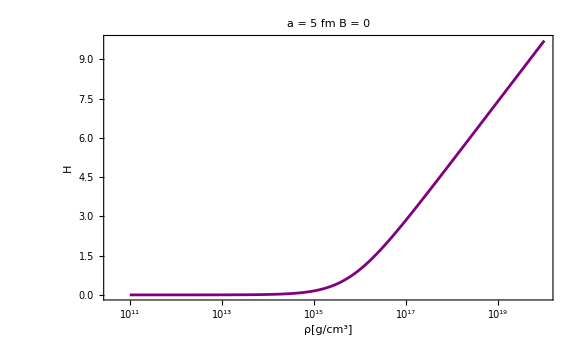

```mathematica
ListLogLinearPlot[Transpose[{Rhodat,Hdat}],Joined->True,Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,
PlotLabel->Style["a = 5 fm    B = 0",Black,Bold,16],
FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["H",Black,Bold,16]
},PlotRange->{{0,Automatic},{0,Automatic}}
]
```

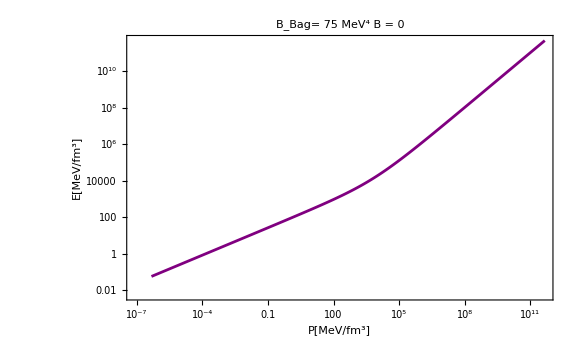

```mathematica
(*Aqui ploteamos la EoS solo por placer*)
ListLogLogPlot[EvsPdat/197.3^3,Joined->True,Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,
PlotLabel->Style["B_Bag= 75 MeV^4    B = 0",Black,Bold,16],
FrameLabel->{
Style["P[MeV/fm^3]",Black,Bold,16],
Style["E[MeV/fm^3]",Black,Bold,16]
},PlotRange->{{0,Automatic},Automatic}
]
```

```mathematica
Subscript[e, surf]= Energy[Pmin];
Print["La energia en la superficie de la estrella sera  ", Subscript[e, surf]/197.3^3, "  MeV/fm^3"]
```

La energia en la superficie de la estrella sera  0.0560748  MeV/fm^3

```mathematica
(*Para convertir las distancias*)
km = 5.07 * 10^15(*MeV^-1*);
cm = 5.07*10^10(*MeV^-1*);
(*Para convertir las distancias*)
g = 5.61*10^26(*MeV*);
(*Masa del Sol*)
M_☉= 1.1158*10^60(*MeV*);
(*Constante de gravitacion universal*)
G = 6.711 * 10^-45(*MeV^-2*);
```

```mathematica
(*Estas son las condiciones iniciales para las ecuaciones diferenciales que vamos a resolver*)
CondicionesIniciales= {
M[Subscript[r, 0]] == 4/3 π Subscript[r, 0]^3 ϵ[Subscript[P, 0]],
P[Subscript[r, 0]] == Subscript[P, 0] - 4π G ϵ[Subscript[P, 0]] (Subscript[P, 0] + ϵ[Subscript[P, 0]])Subscript[r, 0],
y[Subscript[r, 0]] == 2,
J0[Subscript[r, 0]] == 8/15 π Subscript[r, 0]^5(ϵ[Subscript[P, 0]]+Subscript[P, 0])ⅇ^H[Subscript[P, 0]],
Mb[Subscript[r, 0]] == 4/3 π Subscript[r, 0]^3 ρ[Subscript[P, 0]]  g/cm^3
};
```

```mathematica
(*Definimos las expresiones para F y Q de la ecuacion de y*)
F[r]=  (1+4 G π r^2 (P[r]-ϵ[P[r]]))/(1-(2 G M[r])/r);
Q[r]=-1/r^2- ((1+8 G π r^2 P[r])^2)/(r^2(1-(2 G M[r])/r)^2)- (4(1-(2 G M[r])/r)^-1)/r^2+(4 G π  (13 P[r]+5 ϵ[P[r]]+(P[r]+ϵ[P[r]]) ϵ'[P[r]]))/(1-(2 G M[r])/r);
```

```mathematica
(*Resolveremos la ecuacion diferencial en el espacio Subscript[r, min]< r < Subscript[r, max]*)
(*Para 0 < r ≤ Subscript[r, min] usamos la expansion en taylor*)
rmin = 10^-4 km;
rmax = 30km;
```

```mathematica
(*Definimos el sistema de ecuaciones*)
ODEsystem = {
M'[r] == 4π r^2 ϵ[P[r]],
P'[r] ==-(G(P[r] + ϵ[P[r]])(M[r] + 4π r^3 P[r]))/((1- 2(G M[r])/r)r^2),
y'[r] == - (y[r]^2+ F[r]y[r] + r^2 Q[r])/r,
J0'[r] == 8/3 π r^4 ⅇ^H[P[r]](P[r] + ϵ[P[r]])/(√(1- 2(G M[r])/r)),
Mb'[r] == (4π r^2 ρ[P[r]])/(√(1-(2G M[r])/r))g/cm^3,
WhenEvent[P[r] == Pmin, 
StarRadius = r; 
StarMass = M[r]; 
yR = y[r] - (4 π r^3)/M[r] Subscript[e, surf];
J = J0[r]/(√(1- 2(G M[r])/r));
StarCompacity= (G M[r])/r;
z = 1/(√(1-2G M[r]/r))-1;
StarRestMass= Mb[r];
 "StopIntegration"]
};
```

```mathematica
(*Aqui empaquetamos todas las ecuaciones en una misma lista y le damos un valor a la presion central*)
CentralPressure = 10^10;
eqs = ODEsystem∪CondicionesIniciales/. {ϵ-> Energy,H-> HeatFunction, Subscript[P, 0]-> CentralPressure, Subscript[r, 0]-> rmin,ρ-> BarionicDensity};
(*Aqui limpiamos los nombres de las variables que seran el radio y la mas de la estrellas*)
Clear[StarRadius]; Clear[StarMass];Clear[yR];Clear[StarCompacity];Clear[J];Clear[z];Clear[StarRestMass];
(*Aqui resolvemos el sistema*)
sol=NDSolve[eqs,{P,M,y,J0},{r,rmin, 30km},Method->"BDF"][[1]]
(*Aqui extremos las soluciones que estan metidas en sol*)
solP = P/. sol;
solM = M/. sol;
solY = y/. sol;
solJ0 = J0/. sol;
(*Para calcular el numero de Love usamos:*)
Subscript[k, 2]= (8 (1-2 c)^2 c^5 (2+2 c (-1+yR)-yR))/(5 (2 c (6-3 yR+c (3 (-8+5 yR)+2 c (13-11 yR+c (-2+3 yR+2 c (1+yR)))))-3 (1-2 c)^2 (2+2 c (-1+yR)-yR) Log[1/(1-2 c)]))/. c-> StarCompacity
Λ = 2/3 Subscript[k, 2]/c^5/. c-> StarCompacity
```

{P→InterpolatingFunction[…],M→InterpolatingFunction[…],y→InterpolatingFunction[…],J0→InterpolatingFunction[…]}

0.0211569

21.1606

```mathematica
(*Veamos cuanto dieron las cosas*)
Print["R =   ", StarRadius/km," km"]
Print["M =   ", StarMass/(M_☉)," M_☉"]
Print["M_B =   ", StarRestMass/(M_☉)," M_☉"]
Print["J =   ", J/(M_☉ km^2)," M_☉km^2"]
Print["ν_s =   ", Log[1- 2G StarMass/StarRadius]]

Print["y_R =   ", yR]
Print["C =   ", StarCompacity]
Print["z =   ", z]
Print["k_2 =   ", Subscript[k, 2]]
Print["Λ =   ", Λ]
```

R =   7.33242 km

M =   1.14987 M_☉

M_B =   1.25763 M_☉

J =   35.7441 M_☉km^2

ν_s =   -0.622185

y_R =   1.71697

C =   0.231615

z =   0.364915

k_2 =   0.0211569

Λ =   21.1606

```mathematica
BarionicDensity[CentralPressure]
```

5.29944×10^15

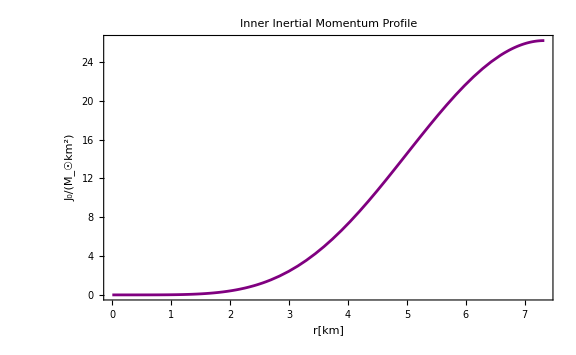

```mathematica
(*Grafiquemos el perfil interior de Subscript[J, 0]*)
Plot[solJ0[r km]/(M_☉km^2),{r, rmin/km,StarRadius/km},Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,
PlotLabel->Style["Inner Inertial Momentum Profile",Black,Bold,16],
FrameLabel->{
Style["r[km]",Black,Bold,16],
Style["J_0/(M_☉km^2)",Black,Bold,16]
}]
```

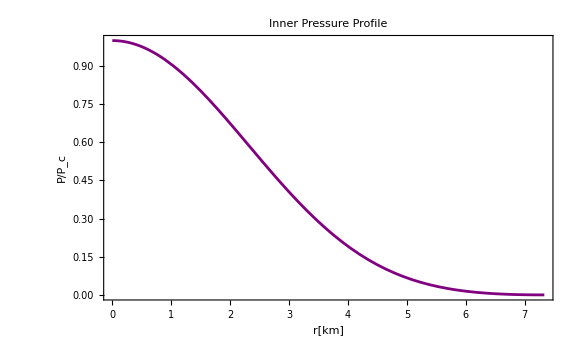

```mathematica
(*Grafiquemos el perfil interior de presion*)
Plot[solP[r km]/CentralPressure,{r, rmin/km,StarRadius/km},Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,
PlotLabel->Style["Inner Pressure Profile",Black,Bold,16],
FrameLabel->{
Style["r[km]",Black,Bold,16],
Style["P/P_c",Black,Bold,16]
}]
```

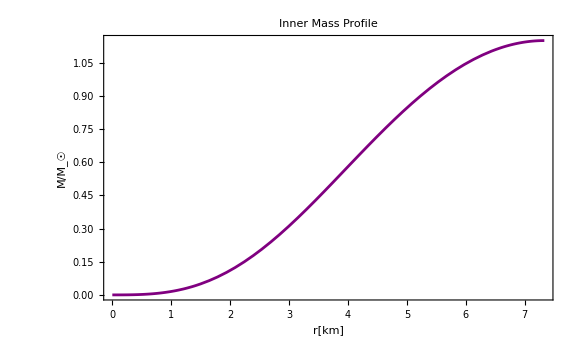

```mathematica
(*Grafiquemos el perfil interior de masa*)
Plot[solM[r km]/M_☉,{r, rmin/km,StarRadius/km},Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,
PlotLabel->Style["Inner Mass Profile",Black,Bold,16],
FrameLabel->{
Style["r[km]",Black,Bold,16],
Style["M/M_☉",Black,Bold,16]
}]
```

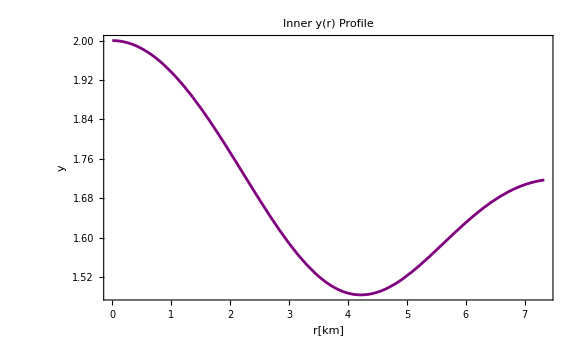

```mathematica
(*Grafiquemos el perfil interior de y*)
Plot[solY[r km],{r, rmin/km,StarRadius/km},Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,
PlotLabel->Style["Inner y(r) Profile",Black,Bold,16],
FrameLabel->{
Style["r[km]",Black,Bold,16],
Style["y",Black,Bold,16]
}]
```

```mathematica
(*Ahora debemos hacer esto mismo para toda una secuencia*)
(*Lista donde guardaremos los obervable*)
```

```mathematica
Length[Pdat]
```

301

```mathematica
Obs = {};
For[ i = 1, i ≤ Length[Pdat], i++  ,
CentralPressure = Pdat[[i]];
If[CentralPressure≤ 0 || Rhodat[[i]] ≤ 10^14, Continue[]];
eqs = ODEsystem∪CondicionesIniciales/. {ϵ-> Energy, Subscript[P, 0]-> CentralPressure, Subscript[r, 0]-> rmin,H-> HeatFunction,ρ-> BarionicDensity};
(*Aqui limpiamos los nombres de las variables que seran el radio y la mas de la estrellas*)
Clear[StarRadius]; Clear[StarMass];Clear[yR];Clear[StarCompacity];Clear[Subscript[k, 2]];Clear[Λ];Clear[z];Clear[StarRestMass];
(*Aqui resolvemos el sistema*)
NDSolve[eqs,{P,M,y},{r,rmin, 30km},Method->"BDF"][[1]];
Subscript[k, 2]= (8 (1-2 c)^2 c^5 (2+2 c (-1+yR)-yR))/(5 (2 c (6-3 yR+c (3 (-8+5 yR)+2 c (13-11 yR+c (-2+3 yR+2 c (1+yR)))))-3 (1-2 c)^2 (2+2 c (-1+yR)-yR) Log[1/(1-2 c)]))/. c-> StarCompacity;
Λ = 2/3 Subscript[k, 2]/c^5/. c-> StarCompacity;
AppendTo[Obs,{Edat[[i]]/197.3^3, StarMass/(M_☉), StarRadius/km, StarCompacity, Subscript[k, 2],Λ, J/(M_☉km^2),z,Rhodat[[i]], StarRestMass/(M_☉)}];
]
```

Clear::ssym: k_2 is not a symbol or a valid string pattern.

General::stop: Further output of Clear::ssym will be suppressed during this calculation.

```mathematica
(*Ahora exportamos la tabla con los observables a un archivo cuyo nombre sera obs_+filename*)
Export[ "obs_"<>filename,Obs]
(*En dicho archivo apareceran 10 columnas dedicadas a:

E[MeV/fm^3] M/M_☉ R[km]  C  Subscript[k, 2]  Λ  I/(M☉ km^2) z ρ[g/cm^3] Subscript[M, B]/M_☉

*)
Length[Obs]
```

obs_bosons_T0_B0_a5.dat

1041

```mathematica
(*Extraemos los datos*)
Masses = Obs[[All,2]];
Energies = Obs[[All,1]];
Radii = Obs[[All,3]];
Compacities = Obs[[All,4]];
k2s = Obs[[All,5]];
Λs = Obs[[All,6]];
Js = Obs[[All,7]];
Zs = Obs[[All,8]];
Rhos = Obs[[All,9]];
Mbs = Obs[[All,10]];
```

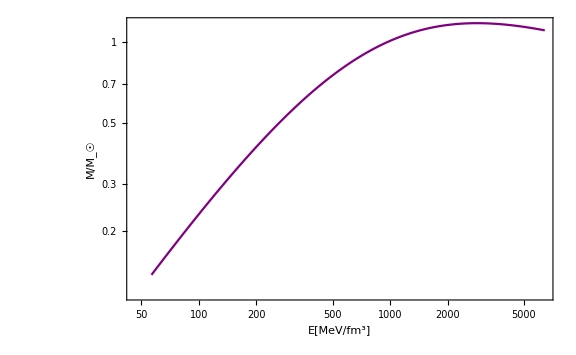

```mathematica
(*graficas*)
ListLogLogPlot[Transpose[{Energies,Masses}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,
PlotStyle->Purple,

FrameLabel->{
Style["E[MeV/fm^3]",Black,Bold,16],
Style["M/M_☉",Black,Bold,16]
}, Joined->True]
```

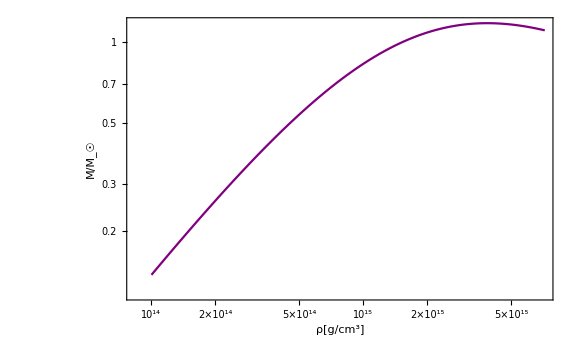

```mathematica
ListLogLogPlot[Transpose[{Rhos ,Masses}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,
PlotStyle->Purple,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["M/M_☉",Black,Bold,16]
}, Joined->True]
```

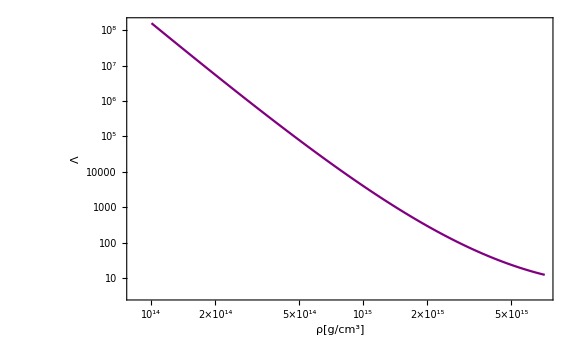

```mathematica
ListLogLogPlot[Transpose[{Rhos,Λs}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,
PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["Λ",Black,Bold,16]
}, Joined->True]
```

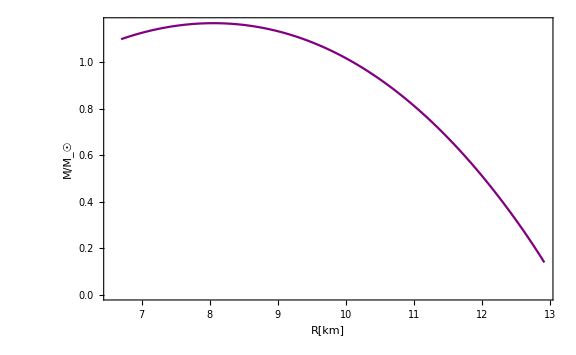

```mathematica
ListPlot[Transpose[{Radii,Masses}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["R[km]",Black,Bold,16],
Style["M/M_☉",Black,Bold,16]
}, Joined->True]
```

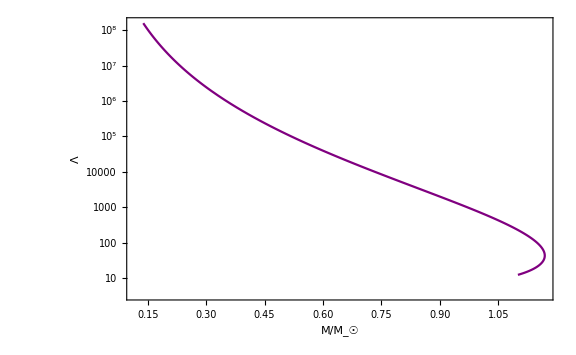

```mathematica
ListLogPlot[Transpose[{Masses,Λs}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["M/M_☉",Black,Bold,16],
Style["Λ",Black,Bold,16]
}, Joined->True]
```

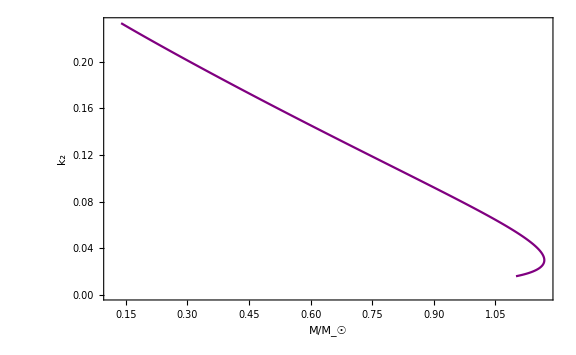

```mathematica
ListPlot[Transpose[{Masses,k2s}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["M/M_☉",Black,Bold,16],
Style[" k_2",Black,Bold,16]
}, Joined->True]
```

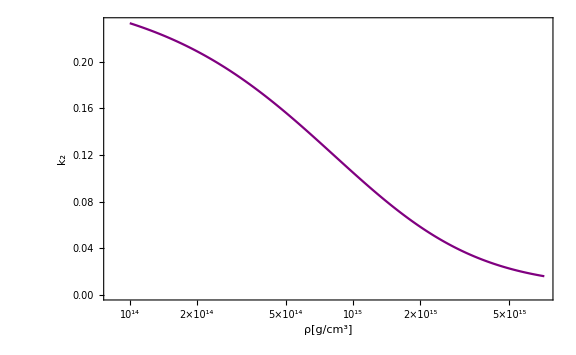

```mathematica
ListLogLinearPlot[Transpose[{Rhos,k2s}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style[" k_2",Black,Bold,16]
}, Joined->True]
```

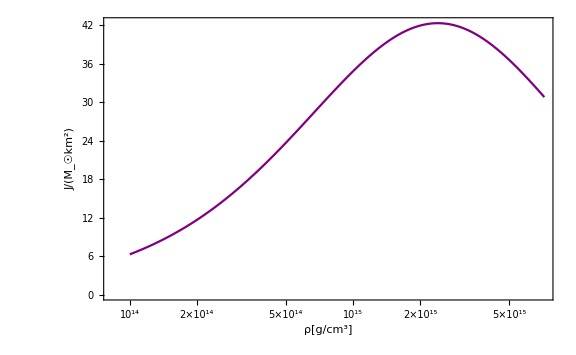

```mathematica
ListLogLinearPlot[Transpose[{Rhos,Js}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["J/(M_☉km^2)",Black,Bold,16]
}, Joined->True]
```

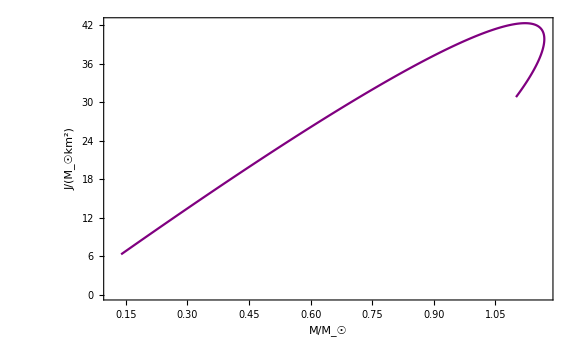

```mathematica
ListPlot[Transpose[{Masses,Js}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["M/M_☉",Black,Bold,16],
Style[" J/(M_☉km^2)",Black,Bold,16]
}, Joined->True]
```

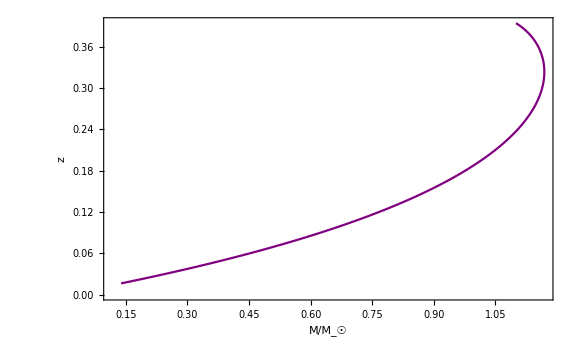

```mathematica
ListPlot[Transpose[{Masses,Zs}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["M/M_☉",Black,Bold,16],
Style["z",Black,Bold,16]
}, Joined->True]
```

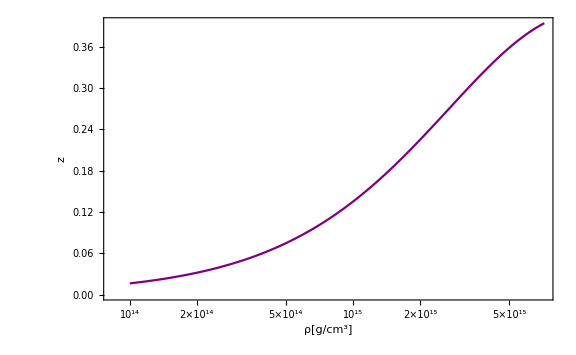

```mathematica
ListLogLinearPlot[Transpose[{Rhos,Zs}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["z",Black,Bold,16]
}, Joined->True]
```

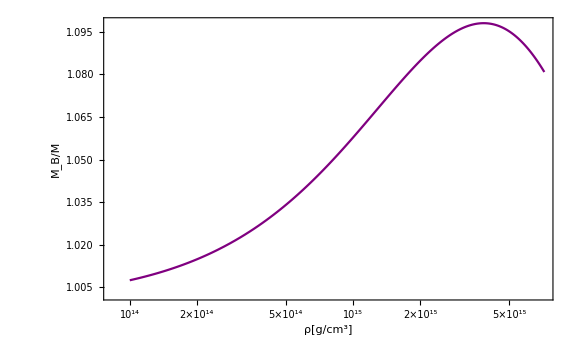

```mathematica
ListLogLinearPlot[Transpose[{Rhos,Mbs/Masses}],Frame->True,FrameStyle->Directive[Black,Bold,16],ImageSize->Large,PlotStyle->Purple,PlotRange->All,

FrameLabel->{
Style["ρ[g/cm^3]",Black,Bold,16],
Style["M_B/M",Black,Bold,16]
}, Joined->True]
```